## Simplified FK of SRSPM

```mathematica
SetDirectory[NotebookDirectory[]]
(*<<ed5314utils_en.m*)
```

/home/aditya/Aditya/Academic/IIT Madras ED/Robotics Lab/Manipulators Group/Aditya Kolte/Root tracking methods

```mathematica
rotZ[θ_]:={{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}};
```

```mathematica
sub={b2x->1.107915,b2y->0,b2z->0,b3x->0.549094,b3y->0.756063,b3z->0,b4x->0.735077,b4y->-0.223935,b4z->0.525991,b5x->0.514188,b5y->-0.526063,b5z->-0.368418,b6x->0.590473,b6y->0.094733,b6z->-0.205018,t2x->0.542805,t2y->0,t2z->0,t3x->0.956919,t3y->-0.528915,t3z->0,t4x->0.665885,t4y->-0.353482,t4z->1.402538,t5x->0.478359,t5y->1.158742,t5z->0.107672,t6x->-0.137087,t6y->-0.235121,t6z->0.353913}
len={l1->1,l2->0.645275,l3->1.086284,l4->1.503439,l5->1.281933,l6->0.771071}
```

{b2x→1.10792,b2y→0,b2z→0,b3x→0.549094,b3y→0.756063,b3z→0,b4x→0.735077,b4y→-0.223935,b4z→0.525991,b5x→0.514188,b5y→-0.526063,b5z→-0.368418,b6x→0.590473,b6y→0.094733,b6z→-0.205018,t2x→0.542805,t2y→0,t2z→0,t3x→0.956919,t3y→-0.528915,t3z→0,t4x→0.665885,t4y→-0.353482,t4z→1.40254,t5x→0.478359,t5y→1.15874,t5z→0.107672,t6x→-0.137087,t6y→-0.235121,t6z→0.353913}

{l1→1,l2→0.645275,l3→1.08628,l4→1.50344,l5→1.28193,l6→0.771071}

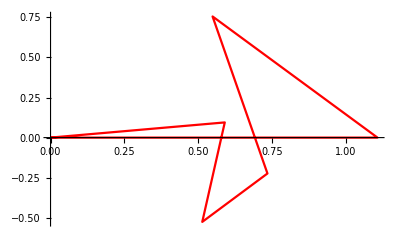

```mathematica
(*Fixed Platform*)
o1={0,0,0};
o2={b2x,b2y,b2z};
o3={b3x,b3y,b3z};
o4={b4x,b4y,b4z};
o5={b5x,b5y,b5z};
o6={b6x,b6y,b6z};
o={o1,o2,o3,o4,o5,o6,o1};
(*ListLinePlot[(o/.sub)[[;;, 1;;2]],PlotStyle->Red]
oj={bjx,bjy,bjz};*)
```

```mathematica
(*Moving platform*)
p1={0,0,0};
p2={t2x,t2y,t2z};
p3={t3x,t3y,t3z};
p4={t4x,t4y,t4z};
p5={t5x,t5y,t5z};
p6={t6x,t6y,t6z};
p={p1,p2,p3,p4,p5,p6,p1};
(*ListLinePlot[(p/.sub)[[;;, 1;;2]]]
pj={tjx,tjy,tjz};*)
```

```mathematica
Cmat={{0,-c3,c2},{c3,0,-c1},{-c2,c1,0}}
```

{{0,-c3,c2},{c3,0,-c1},{-c2,c1,0}}

```mathematica
Rmat=Simplify[(IdentityMatrix[3]+Cmat).Inverse[(IdentityMatrix[3]-Cmat)]];
```

```mathematica
xvec={x,y,z};
```

```mathematica
p1o=xvec+Rmat.p1;
p2o=xvec+Rmat.p2;
p3o=xvec+Rmat.p3;
p4o=xvec+Rmat.p4;
p5o=xvec+Rmat.p5;
p6o=xvec+Rmat.p6;
(*pjo=xvec+Rmat.pj;*)
```

```mathematica
p2o
```

{((1+c1^2-c2^2-c3^2) t2x)/(1+c1^2+c2^2+c3^2)+((2 c1 c2-2 c3) t2y)/(1+c1^2+c2^2+c3^2)+(2 (c2+c1 c3) t2z)/(1+c1^2+c2^2+c3^2)+x,(2 (c1 c2+c3) t2x)/(1+c1^2+c2^2+c3^2)+((1-c1^2+c2^2-c3^2) t2y)/(1+c1^2+c2^2+c3^2)-(2 (c1-c2 c3) t2z)/(1+c1^2+c2^2+c3^2)+y,(2 (-c2+c1 c3) t2x)/(1+c1^2+c2^2+c3^2)+(2 (c1+c2 c3) t2y)/(1+c1^2+c2^2+c3^2)+((1-c1^2-c2^2+c3^2) t2z)/(1+c1^2+c2^2+c3^2)+z}

```mathematica
eq1=(p1o-o1).(p1o-o1)-l1^2
```

-l1^2+x^2+y^2+z^2

```mathematica
(*monoprod[{a_,b_}]:=a.b;
eqj=FullSimplify[monoprod[FullSimplify[monopoly[Factor[(pjo-oj).(pjo-oj)-lj^2][[3]],{bjx,bjy,bjz,tjx,tjy,tjz,lj}]]/.{ (x^2+y^2+z^2)-> w,1+c1^2+c2^2+c3^2-> c0,-1-c1^2-c2^2-c3^2-> -c0}]];*)
```

```mathematica
eq2=FullSimplify[Factor[(p2o-o2).(p2o-o2)-l2^2][[3]]];
eq3=FullSimplify[Factor[(p3o-o3).(p3o-o3)-l3^2][[3]]];
eq4=FullSimplify[Factor[(p4o-o4).(p4o-o4)-l4^2][[3]]];
eq5=FullSimplify[Factor[(p5o-o5).(p5o-o5)-l5^2][[3]]];
eq6=FullSimplify[Factor[(p6o-o6).(p6o-o6)-l6^2][[3]]];
```

```mathematica
os = Table[Symbol["o"<>ToString[i]],{i, 6}];
ps = Table[Symbol["p"<>ToString[i]],{i, 6}];
```

```mathematica
Join[ps, os]//Flatten
```

{0,0,0,t2x,t2y,t2z,t3x,t3y,t3z,t4x,t4y,t4z,t5x,t5y,t5z,t6x,t6y,t6z,0,0,0,b2x,b2y,b2z,b3x,b3y,b3z,b4x,b4y,b4z,b5x,b5y,b5z,b6x,b6y,b6z}

```mathematica
eq = Table[Symbol["eq"<>ToString[i]],{i, 6}];
```

```mathematica
f = Table[Symbol["f"<>ToString[i]],{i, 6}];
```

```mathematica
Thread[f==eq];
```

```mathematica
nsol=Timing[NSolve[N[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len),50]=={0,0,0,0,0,0},{x,y,z,c1,c2,c3},Method-> "HomotopyContinuation"]];
```

```mathematica
Dimensions[nsol[[2]]]
nsol[[2]]//MatrixForm
```

{40,6}

(x→0.958098 | y→-0.284039 | z→-0.0370116 | c1→-41.7087 | c2→1.46573 | c3→-53.9009
x→0.667532 | y→0.738317 | z→-0.0963786 | c1→-14.61 | c2→17.7118 | c3→-7.94613
x→0.870078 | y→-0.451122 | z→-0.198631 | c1→16.356 | c2→-1.48865 | c3→18.0985
x→0.998523 | y→0.0311963 | z→0.0444774 | c1→1.39775 | c2→11.3167 | c3→-7.18144
x→0.991613 | y→-0.127016 | z→0.0238671 | c1→-4.80989 | c2→-0.206662 | c3→-7.13794
x→0.995368 | y→-0.0511993 | z→0.0813756 | c1→-1.46984 | c2→-9.18994 | c3→5.08597
x→0.707963 | y→0.685868 | z→-0.168443 | c1→-3.65242 | c2→5.0327 | c3→-2.70288
x→0.999628 | y→0.0261758 | z→-0.0077237 | c1→0.71941 | c2→4.30632 | c3→-3.27645
x→0.719131 | y→0.633883 | z→-0.284681 | c1→-1.91893 | c2→2.64219 | c3→-1.78087
x→0.539848 | y→0.67884 | z→0.497734 | c1→4.2725 | c2→-1.10003 | c3→-0.310949
x→0.521848 | y→0.81072 | z→0.265345 | c1→3.38638 | c2→-1.34558 | c3→0.120505
x→0.998901 | y→-0.0415643 | z→-0.0216517 | c1→0.854663 | c2→2.61742 | c3→-2.52117
x→0.689418 | y→0.593656 | z→-0.41506 | c1→-1.45692 | c2→1.66043 | c3→-1.42532
x→0.82508 | y→-0.318926 | z→0.4664 | c1→23.2235 | c2→-8.38791 | c3→-29.1595
x→0.832285 | y→-0.282752 | z→0.476816 | c1→-8.0004 | c2→4.88638 | c3→11.0376
x→0.484612 | y→-0.873935 | z→-0.0372779 | c1→-2.76293 | c2→-0.821946 | c3→-0.0848068
x→0.442199 | y→-0.713494 | z→-0.543494 | c1→-1.63365 | c2→-0.755714 | c3→-0.497624
x→0.53506 | y→-0.749596 | z→-0.389637 | c1→-1.92829 | c2→-1.3897 | c3→-0.865492
x→0.443038 | y→-0.558622 | z→-0.701185 | c1→-1.37069 | c2→-0.733475 | c3→-0.632058
x→0.7811 | y→0.0687982 | z→-0.620604 | c1→1.06641 | c2→-2.19858 | c3→1.53425
x→0.458734 | y→-0.373481 | z→-0.806272 | c1→-1.16137 | c2→-0.712906 | c3→-0.758101
x→0.891375 | y→-0.079827 | z→-0.446182 | c1→0.418169 | c2→-2.50974 | c3→1.69303
x→0.485481 | y→-0.200818 | z→-0.85087 | c1→-1.00711 | c2→-0.698564 | c3→-0.869763
x→0.477891 | y→-0.781099 | z→-0.401876 | c1→-1.33685 | c2→-0.41715 | c3→0.300645
x→0.534003 | y→0.00617399 | z→-0.84546 | c1→-0.840592 | c2→-0.686379 | c3→-1.01544
x→0.585911 | y→0.161498 | z→-0.79412 | c1→-0.710841 | c2→-0.681836 | c3→-1.1499
x→0.854376 | y→-0.294203 | z→0.428353 | c1→-2.68979 | c2→2.45163 | c3→4.42175
x→0.679796 | y→0.348061 | z→-0.645547 | c1→-0.503275 | c2→-0.68793 | c3→-1.39335
x→0.489122 | y→0.69623 | z→-0.525379 | c1→1.3581 | c2→-0.497104 | c3→0.330951
x→0.968094 | y→0.236773 | z→-0.0820477 | c1→1.17886 | c2→-0.223564 | c3→1.36845
x→0.903174 | y→-0.418445 | z→0.095812 | c1→-0.343336 | c2→1.4044 | c3→1.98259
x→0.855766 | y→-0.334679 | z→0.394532 | c1→4.93522 | c2→-0.800049 | c3→-6.53719
x→0.955868 | y→-0.0469956 | z→-0.290013 | c1→0.095203 | c2→0.282266 | c3→1.00721
x→0.636112 | y→0.771452 | z→0.0149558 | c1→1.29659 | c2→-0.0173546 | c3→-1.06671
x→0.803268 | y→-0.296007 | z→0.516856 | c1→-1.9372 | c2→-1.44397 | c3→0.465246
x→0.993577 | y→0.0796655 | z→-0.0803592 | c1→-0.256749 | c2→0.0223243 | c3→0.947016
x→0.863326 | y→0.00564402 | z→-0.504616 | c1→0.556083 | c2→0.214152 | c3→0.918104
x→0.993726 | y→0.111786 | z→0.00361272 | c1→-0.386141 | c2→-0.136732 | c3→0.90128
x→0.989132 | y→0.116671 | z→0.0894713 | c1→-0.505993 | c2→-0.312872 | c3→0.859321
x→0.917778 | y→-0.111176 | z→0.381213 | c1→-1.12945 | c2→-1.15566 | c3→0.726784)

```mathematica
Norm[Flatten[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len/.#)] ]&/@nsol[[2]]//MatrixForm(*Residue check*)
```

(4.0481×10^-10
3.51402×10^-10
2.21927×10^-10
5.59652×10^-10
4.99479×10^-9
8.38002×10^-11
1.79744×10^-9
6.12881×10^-9
4.33238×10^-9
8.22574×10^-10
6.42683×10^-10
1.59023×10^-8
3.27641×10^-9
3.03613×10^-6
5.77557×10^-6
1.57937×10^-9
3.47745×10^-10
5.94676×10^-8
3.16898×10^-10
8.80681×10^-10
2.39813×10^-10
1.09594×10^-9
7.63399×10^-10
1.82205×10^-7
1.1797×10^-9
7.05753×10^-10
0.0000116662
6.89182×10^-10
3.09359×10^-10
1.18904×10^-9
1.92038×10^-9
1.14932×10^-8
3.91447×10^-9
7.50631×10^-10
1.45007×10^-7
2.42828×10^-9
5.6198×10^-7
1.10122×10^-8
2.14172×10^-9
2.29898×10^-9)

```mathematica
Select[c3/.nsol[[2]],Abs[Im[#]]≤ 10^-6&](*Reals filter*)
```

{-53.9009,-7.94613,18.0985,-7.18144,-7.13794,5.08597,-2.70288,-3.27645,-1.78087,-0.310949,0.120505,-2.52117,-1.42532,-29.1595,11.0376,-0.0848068,-0.497624,-0.865492,-0.632058,1.53425,-0.758101,1.69303,-0.869763,0.300645,-1.01544,-1.1499,4.42175,-1.39335,0.330951,1.36845,1.98259,-6.53719,1.00721,-1.06671,0.465246,0.947016,0.918104,0.90128,0.859321,0.726784}

## Use these solutions till I figure out how to get the others

```mathematica
reqsol=nsol[[2]];
```

```mathematica
reqsol//MatrixForm
```

(x→0.958098 | y→-0.284039 | z→-0.0370116 | c1→-41.7087 | c2→1.46573 | c3→-53.9009
x→0.667532 | y→0.738317 | z→-0.0963786 | c1→-14.61 | c2→17.7118 | c3→-7.94613
x→0.870078 | y→-0.451122 | z→-0.198631 | c1→16.356 | c2→-1.48865 | c3→18.0985
x→0.998523 | y→0.0311963 | z→0.0444774 | c1→1.39775 | c2→11.3167 | c3→-7.18144
x→0.991613 | y→-0.127016 | z→0.0238671 | c1→-4.80989 | c2→-0.206662 | c3→-7.13794
x→0.995368 | y→-0.0511993 | z→0.0813756 | c1→-1.46984 | c2→-9.18994 | c3→5.08597
x→0.707963 | y→0.685868 | z→-0.168443 | c1→-3.65242 | c2→5.0327 | c3→-2.70288
x→0.999628 | y→0.0261758 | z→-0.0077237 | c1→0.71941 | c2→4.30632 | c3→-3.27645
x→0.719131 | y→0.633883 | z→-0.284681 | c1→-1.91893 | c2→2.64219 | c3→-1.78087
x→0.539848 | y→0.67884 | z→0.497734 | c1→4.2725 | c2→-1.10003 | c3→-0.310949
x→0.521848 | y→0.81072 | z→0.265345 | c1→3.38638 | c2→-1.34558 | c3→0.120505
x→0.998901 | y→-0.0415643 | z→-0.0216517 | c1→0.854663 | c2→2.61742 | c3→-2.52117
x→0.689418 | y→0.593656 | z→-0.41506 | c1→-1.45692 | c2→1.66043 | c3→-1.42532
x→0.82508 | y→-0.318926 | z→0.4664 | c1→23.2235 | c2→-8.38791 | c3→-29.1595
x→0.832285 | y→-0.282752 | z→0.476816 | c1→-8.0004 | c2→4.88638 | c3→11.0376
x→0.484612 | y→-0.873935 | z→-0.0372779 | c1→-2.76293 | c2→-0.821946 | c3→-0.0848068
x→0.442199 | y→-0.713494 | z→-0.543494 | c1→-1.63365 | c2→-0.755714 | c3→-0.497624
x→0.53506 | y→-0.749596 | z→-0.389637 | c1→-1.92829 | c2→-1.3897 | c3→-0.865492
x→0.443038 | y→-0.558622 | z→-0.701185 | c1→-1.37069 | c2→-0.733475 | c3→-0.632058
x→0.7811 | y→0.0687982 | z→-0.620604 | c1→1.06641 | c2→-2.19858 | c3→1.53425
x→0.458734 | y→-0.373481 | z→-0.806272 | c1→-1.16137 | c2→-0.712906 | c3→-0.758101
x→0.891375 | y→-0.079827 | z→-0.446182 | c1→0.418169 | c2→-2.50974 | c3→1.69303
x→0.485481 | y→-0.200818 | z→-0.85087 | c1→-1.00711 | c2→-0.698564 | c3→-0.869763
x→0.477891 | y→-0.781099 | z→-0.401876 | c1→-1.33685 | c2→-0.41715 | c3→0.300645
x→0.534003 | y→0.00617399 | z→-0.84546 | c1→-0.840592 | c2→-0.686379 | c3→-1.01544
x→0.585911 | y→0.161498 | z→-0.79412 | c1→-0.710841 | c2→-0.681836 | c3→-1.1499
x→0.854376 | y→-0.294203 | z→0.428353 | c1→-2.68979 | c2→2.45163 | c3→4.42175
x→0.679796 | y→0.348061 | z→-0.645547 | c1→-0.503275 | c2→-0.68793 | c3→-1.39335
x→0.489122 | y→0.69623 | z→-0.525379 | c1→1.3581 | c2→-0.497104 | c3→0.330951
x→0.968094 | y→0.236773 | z→-0.0820477 | c1→1.17886 | c2→-0.223564 | c3→1.36845
x→0.903174 | y→-0.418445 | z→0.095812 | c1→-0.343336 | c2→1.4044 | c3→1.98259
x→0.855766 | y→-0.334679 | z→0.394532 | c1→4.93522 | c2→-0.800049 | c3→-6.53719
x→0.955868 | y→-0.0469956 | z→-0.290013 | c1→0.095203 | c2→0.282266 | c3→1.00721
x→0.636112 | y→0.771452 | z→0.0149558 | c1→1.29659 | c2→-0.0173546 | c3→-1.06671
x→0.803268 | y→-0.296007 | z→0.516856 | c1→-1.9372 | c2→-1.44397 | c3→0.465246
x→0.993577 | y→0.0796655 | z→-0.0803592 | c1→-0.256749 | c2→0.0223243 | c3→0.947016
x→0.863326 | y→0.00564402 | z→-0.504616 | c1→0.556083 | c2→0.214152 | c3→0.918104
x→0.993726 | y→0.111786 | z→0.00361272 | c1→-0.386141 | c2→-0.136732 | c3→0.90128
x→0.989132 | y→0.116671 | z→0.0894713 | c1→-0.505993 | c2→-0.312872 | c3→0.859321
x→0.917778 | y→-0.111176 | z→0.381213 | c1→-1.12945 | c2→-1.15566 | c3→0.726784)

```mathematica
(* Residue check *)
Norm[Flatten[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len/.#)] ]&/@reqsol
```

{4.0481×10^-10,3.51402×10^-10,2.21927×10^-10,5.59652×10^-10,4.99479×10^-9,8.38002×10^-11,1.79744×10^-9,6.12881×10^-9,4.33238×10^-9,8.22574×10^-10,6.42683×10^-10,1.59023×10^-8,3.27641×10^-9,3.03613×10^-6,5.77557×10^-6,1.57937×10^-9,3.47745×10^-10,5.94676×10^-8,3.16898×10^-10,8.80681×10^-10,2.39813×10^-10,1.09594×10^-9,7.63399×10^-10,1.82205×10^-7,1.1797×10^-9,7.05753×10^-10,0.0000116662,6.89182×10^-10,3.09359×10^-10,1.18904×10^-9,1.92038×10^-9,1.14932×10^-8,3.91447×10^-9,7.50631×10^-10,1.45007×10^-7,2.42828×10^-9,5.6198×10^-7,1.10122×10^-8,2.14172×10^-9,2.29898×10^-9}

### These are solutions for the center of the moving platform

```mathematica
(* Coordinates of the centeroid of the moving platform *)
mpc=Total[{p1,p2,p3,p4,p5,p6}]/6/.sub
```

{0.417813,0.00687067,0.310687}

```mathematica
transformedsol=Table[Inner[Rule,{x,y,z,c1,c2,c3},(Join[({x,y,z}+Rmat.mpc),{c1,c2,c3}]/.reqsol[[ii]]),List],{ii,1,40}];
```

```mathematica
(* x y z c1 c2 c3 *)
```

```mathematica
transformedsol//MatrixForm
```

(x→1.15393 | y→-0.316567 | z→0.444377 | c1→-41.7087 | c2→1.46573 | c3→-53.9009
x→0.687564 | y→0.229292 | z→-0.20424 | c1→-14.61 | c2→17.7118 | c3→-7.94613
x→1.13222 | y→-0.511617 | z→0.247197 | c1→16.356 | c2→-1.48865 | c3→18.0985
x→0.60031 | y→-0.207759 | z→-0.19104 | c1→1.39775 | c2→11.3167 | c3→-7.18144
x→1.12599 | y→-0.15005 | z→0.526416 | c1→-4.80989 | c2→-0.206662 | c3→-7.13794
x→0.510594 | y→-0.158683 | z→-0.0754146 | c1→-1.46984 | c2→-9.18994 | c3→5.08597
x→0.737825 | y→0.18 | z→-0.288222 | c1→-3.65242 | c2→5.0327 | c3→-2.70288
x→0.665162 | y→-0.276009 | z→-0.268413 | c1→0.71941 | c2→4.30632 | c3→-3.27645
x→0.815826 | y→0.131784 | z→-0.383114 | c1→-1.91893 | c2→2.64219 | c3→-1.78087
x→0.828226 | y→0.351017 | z→0.213988 | c1→4.2725 | c2→-1.10003 | c3→-0.310949
x→0.787701 | y→0.392919 | z→0.104391 | c1→3.38638 | c2→-1.34558 | c3→0.120505
x→0.701514 | y→-0.367164 | z→-0.298576 | c1→0.854663 | c2→2.61742 | c3→-2.52117
x→0.893227 | y→0.115786 | z→-0.450325 | c1→-1.45692 | c2→1.66043 | c3→-1.42532
x→0.423175 | y→-0.359071 | z→0.137763 | c1→23.2235 | c2→-8.38791 | c3→-29.1595
x→0.423004 | y→-0.216621 | z→0.161764 | c1→-8.0004 | c2→4.88638 | c3→11.0376
x→0.805467 | y→-0.493326 | z→-0.190023 | c1→-2.76293 | c2→-0.821946 | c3→-0.0848068
x→0.720784 | y→-0.300049 | z→-0.393178 | c1→-1.63365 | c2→-0.755714 | c3→-0.497624
x→0.680183 | y→-0.283153 | z→-0.209325 | c1→-1.92829 | c2→-1.3897 | c3→-0.865492
x→0.683107 | y→-0.17955 | z→-0.436962 | c1→-1.37069 | c2→-0.733475 | c3→-0.632058
x→0.511615 | y→-0.297929 | z→-0.36756 | c1→1.06641 | c2→-2.19858 | c3→1.53425
x→0.649534 | y→-0.0491601 | z→-0.446337 | c1→-1.16137 | c2→-0.712906 | c3→-0.758101
x→0.456588 | y→-0.305464 | z→-0.269576 | c1→0.418169 | c2→-2.50974 | c3→1.69303
x→0.624636 | y→0.0638483 | z→-0.424573 | c1→-1.00711 | c2→-0.698564 | c3→-0.869763
x→0.657678 | y→-0.300969 | z→-0.492948 | c1→-1.33685 | c2→-0.41715 | c3→0.300645
x→0.599808 | y→0.18916 | z→-0.36242 | c1→-0.840592 | c2→-0.686379 | c3→-1.01544
x→0.582547 | y→0.274032 | z→-0.285724 | c1→-0.710841 | c2→-0.681836 | c3→-1.1499
x→0.462097 | y→-0.103182 | z→0.144152 | c1→-2.68979 | c2→2.45163 | c3→4.42175
x→0.556275 | y→0.355792 | z→-0.139756 | c1→-0.503275 | c2→-0.68793 | c3→-1.39335
x→0.800269 | y→0.309308 | z→-0.368469 | c1→1.3581 | c2→-0.497104 | c3→0.330951
x→1.20839 | y→0.233403 | z→0.379894 | c1→1.17886 | c2→-0.223564 | c3→1.36845
x→0.677638 | y→0.0358921 | z→-0.0218846 | c1→-0.343336 | c2→1.4044 | c3→1.98259
x→0.447844 | y→-0.466039 | z→0.0987511 | c1→4.93522 | c2→-0.800049 | c3→-6.53719
x→1.04429 | y→0.419907 | z→-0.0771134 | c1→0.095203 | c2→0.282266 | c3→1.00721
x→0.580822 | y→0.321938 | z→-0.241992 | c1→1.29659 | c2→-0.0173546 | c3→-1.06671
x→0.746412 | y→0.201062 | z→0.372525 | c1→-1.9372 | c2→-1.44397 | c3→0.465246
x→0.952896 | y→0.568392 | z→0.0946648 | c1→-0.256749 | c2→0.0223243 | c3→0.947016
x→1.14312 | y→0.298004 | z→-0.176926 | c1→0.556083 | c2→0.214152 | c3→0.918104
x→0.90284 | y→0.597119 | z→0.168942 | c1→-0.386141 | c2→-0.136732 | c3→0.90128
x→0.846296 | y→0.593848 | z→0.241266 | c1→-0.505993 | c2→-0.312872 | c3→0.859321
x→0.664573 | y→0.343378 | z→0.360976 | c1→-1.12945 | c2→-1.15566 | c3→0.726784)

```mathematica
(*Bertini is also able to solve the above problem. So shifting to Bertini from now on*)
```

```mathematica
bval = N[o/.sub]
base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
Show[base]
```

{{0.,0.,0.},{1.10792,0.,0.},{0.549094,0.756063,0.},{0.735077,-0.223935,0.525991},{0.514188,-0.526063,-0.368418},{0.590473,0.094733,-0.205018},{0.,0.,0.}}

-Graphics3D-

```mathematica
(*Changing the plotting code*)
```

```mathematica
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis},
(*Base and top plate*)
bval = N[o/.sub]
(*aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];
*)
base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
(*top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];*)
(*Links*)
(*lbinks = Table[Graphics3D[{Purple,Opacity[0.3],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, aval[[i]]-direction[[i]]*la/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis]
*)
Show[base]
]
```

```mathematica
plotsrspm[{0}]
```

-Graphics3D-